lpw harmonic transformation to lab frame

```mathematica
(* Mathematica notebook for analysis of harmonic transformation to lab frame. Following [Gibbon]'s lecture 4
  date : 16/02/2019
  author: Óscar L. Amaro
*)
```

```mathematica
ωL=(m ω0)/(1+a0^2/2 Sin[θL/2]^2)
```

(m ω0)/(1+1/2 a0^2 Sin[θL/2]^2)

```mathematica
Da0=(γ0/(1+a0^2/2 Sin[θL/2]^2))^4
```

γ0^4/((1+1/2 a0^2 Sin[θL/2]^2)^4)

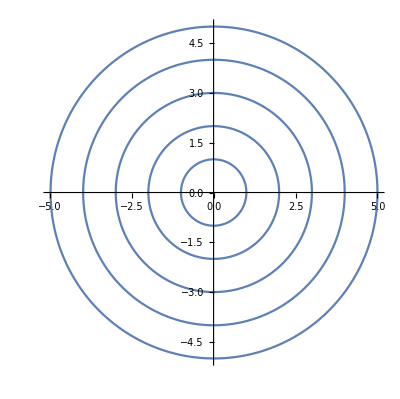

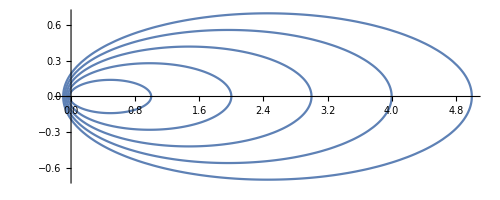

```mathematica
(*(55)*)

a0=0.1;ω0=1;
Show[Table[PolarPlot[(m ω0)/(1+a0^2/2 Sin[θL/2]^2),{θL,0,2 Pi}],{m,1,5}]]
Clear[a0,ω0]

a0=10;ω0=1;
Show[Table[PolarPlot[(m ω0)/(1+a0^2/2 Sin[θL/2]^2),{θL,0,2 Pi}],{m,1,5}]]
Clear[a0,ω0]
```

```mathematica
dPdΩ=Function[{θ,m},γ0^2/(2 a0^2)Cot[θ]^2  BesselJ[m,√2 a0/γ0 m Sin[θ]]^2+(a0^2 m^2 (BesselJ[-1+m,(√2 a0 m Sin[θ])/γ0]-BesselJ[1+m,(√2 a0 m Sin[θ])/γ0])^2 Cos[θ]^2)/(2 γ0^2)];
```

```mathematica
(*for a0·ω0=cte, we have proportionality*)
γ0=10;
dima0=12;
dimm=40;

lst=Table[{0,0},{a0,1,dima0}];

For[a0=1,a0<dima0,a0++;
lstmax=Table[FindMaximum[dPdΩ[θ,m],{θ,0.01,π}][[1]],{m,1,15}];
max=Max[lstmax];
pos=Position[lstmax,max][[1,1]];
lst[[a0,1]]=a0;
lst[[a0,2]]=pos;
]
```

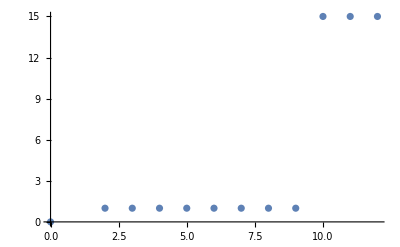

```mathematica
lst;
ListPlot[lst]
```

```mathematica
Show[Table[Plot[dPdΩ[θ,m],{θ,0.01,π},PlotRange->All],{m,1,1}]];

Show[Table[Plot[dPdΩ[θ,m],{θ,0.01,π},PlotRange->All],{m,2,2}]];

Show[Table[Plot[dPdΩ[θ,m],{θ,0.01,π},PlotRange->All],{m,3,3}]];
```

```mathematica
tbl=Table[PolarPlot[dPdΩ[θ,1,a0],{θ,0.01,2π},ImageSize->600,Axes->False],{a0,1,100}];
```

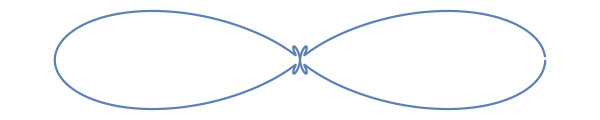

```mathematica
tbl[[20]]
```

```mathematica
ListAnimate[tbl,Alignment->Center]
```

```mathematica
Export["firstharmonic.gif",%]
```

test.gif

lpw power

```mathematica
(* Mathematica notebook for power analysis of harmonics in linear polarized plane wave. Following [Gibbon]'s lecture 4
  date : 20/04/2019
  author: Óscar L. Amaro
*)
```

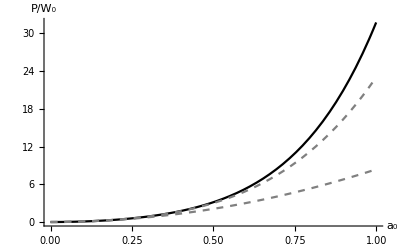

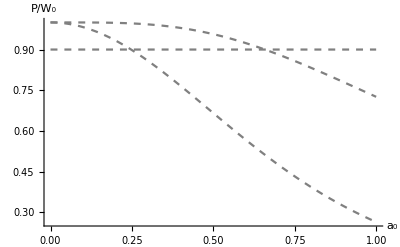

```mathematica
(*leading 3 terms*)
f[a0_]:=(8π)/3 a0^2+(14π)/3 a0^4+(621π)/224 a0^6
(*compare contribution of each term up to Subscript[a, 0]~1*)
Plot[{f[a0],(8π)/3 a0^2,(8π)/3 a0^2+(14π)/3 a0^4},{a0,0,1},AxesLabel->{"a_0","P/W_0"},PlotRange->All,PlotStyle->{Black,Directive[Gray,Dashed],Directive[Gray,Dashed]}]
(*up to which value of Subscript[a, 0] does each incremented term contribute 90% of the total power. The first harmonic contributes almost interily up to Subscript[a, 0]~0.25, the first two contribute the most up to Subscript[a, 0]~0.65*)
Plot[{((8π)/3 a0^2)/f[a0],((8π)/3 a0^2+(14π)/3 a0^4)/f[a0],0.9},{a0,0,1},AxesLabel->{"a_0","P/W_0"},PlotRange->All,PlotStyle->{Directive[Gray,Dashed],Directive[Gray,Dashed]}]
```

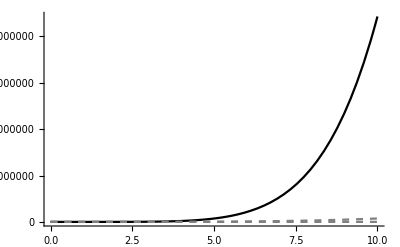

```mathematica
(*one cannot expect the total power to only include up to the third term when Subscript[a, 0] takes larger values*)
Plot[{f[a0],(8π)/3 a0^2,(8π)/3 a0^2+(14π)/3 a0^4},{a0,0,10},PlotRange->All,PlotStyle->{Black,Directive[Gray,Dashed],Directive[Gray,Dashed]}]
```

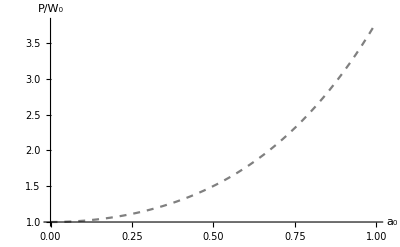

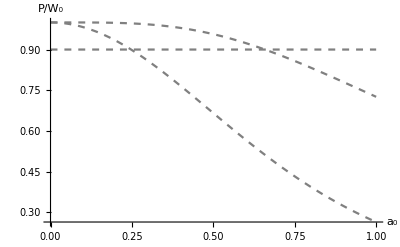

```mathematica
(*testing configuration Subscript[a, 0] Subscript[ω, 0]=cte*)
ω0[a0_,cte_]:=cte/a0
g[a0_,cte_]:=(a0 ω0[a0,cte])^2+7/4(a0^2 ω0[a0,cte])^2+1863/1792(a0^3 ω0[a0,cte])^2
cte=1;
Plot[{g[a0,cte]},{a0,0,1},AxesLabel->{"a_0","P/W_0"},PlotRange->Automatic,PlotStyle->{Black,Directive[Gray,Dashed],Directive[Gray,Dashed]}]

Plot[{(a0 ω0[a0,cte])^2/g[a0,cte],((a0 ω0[a0,cte])^2+7/4(a0^2 ω0[a0,cte])^2)/g[a0,cte],0.9},{a0,0,1},AxesLabel->{"a_0","P/W_0"},PlotRange->Automatic,PlotStyle->{Directive[Gray,Dashed],Directive[Gray,Dashed]}]
```

lpw spectra

```mathematica
(* Mathematica notebook for spectra analysis 2d (ω,θ). Following [Gibbon]'s lecture 4
  date : 24/02/2019
  author: Óscar L. Amaro
*)
```

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
imgsize=400;asp=1;tck=0.01; (*style*)
```

```mathematica
d2I[θ_,m_,γ0_,a0_]:=0.5*((m*a0)/γ0^2)^2*(  ((Cot[θ])/(Sqrt[2]*(a0/γ0))*BesselJ[m,√2 * a0/γ0 * m * Sin[θ]])^2+(Evaluate[(D[BesselJ[m,x],x])/.x->(√2 * a0/γ0 * m * Sin[θ])])^2)
```

```mathematica
(*Δ=1*)
θ=0;θinc=0.05;θmin=0.001;θmax=Pi/2;
mmax=10;minc=1;
γ0=1; (*gamma factor*)
ω0=1; (*fundamental frequency*)
a0=20; (*normalised intensity*)
θ=θmin;
mat=Table[d2I[θ,ω,γ0,a0],{ω,0,mmax,minc}];
```

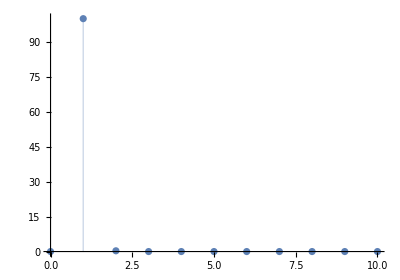

```mathematica
ListPlot[mat,AspectRatio->0.7,ImageSize->imgsize,PlotRange->All,AxesLabel->Automatic,DataRange->{0,har},Filling->Axis](*Simple stem plot, on axis*)
```

```mathematica
Thmin=-Pi;
Thmax=0;
Clear[θ]
mat3=Table[d2I[Abs[θ],ω,γ0,a0],{θ,Thmin,Thmax,0.01},{ω,0.01,mmax,0.1}];
```

```mathematica
mat4=Table[d2I[Abs[θ],ω,γ0,a0]*(γ0/(1+a0^2/2 Sin[θ/2]^2))^4,{θ,Thmin,Thmax,0.01},{ω,0.01,mmax,0.1}];
```

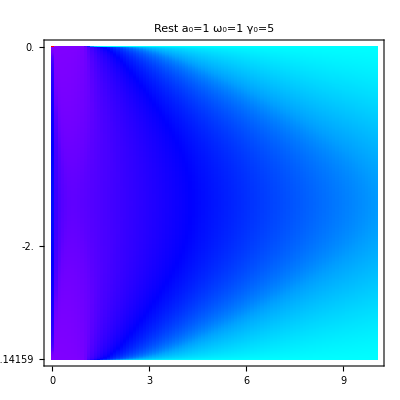

```mathematica
MatrixPlot[mat3,AspectRatio->1,ColorFunction->Hue,PlotLabel->"Rest a_0="<>ToString[a0]<>" ω_0="<>ToString[ω0]<>" γ_0="<>ToString[γ0],DataRange->{{0,mmax},{Thmin,Thmax}},ImageSize->imgsize]
```

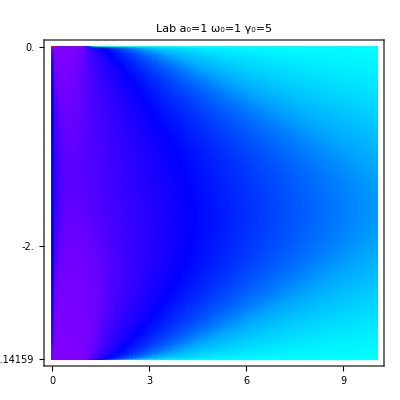

```mathematica
MatrixPlot[mat4,AspectRatio->1,ColorFunction->Hue,PlotLabel->"Lab a_0="<>ToString[a0]<>" ω_0="<>ToString[ω0]<>" γ_0="<>ToString[γ0],DataRange->{{0,mmax},{Thmin,Thmax}},ImageSize->imgsize]
```

```mathematica
Export[ToString[a0]<>"_"<>ToString[ω0]<>"_"<>ToString[γ0]<>".png",%]
```

2000_1_1.png

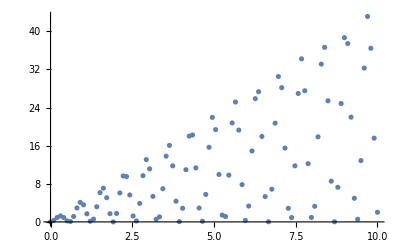

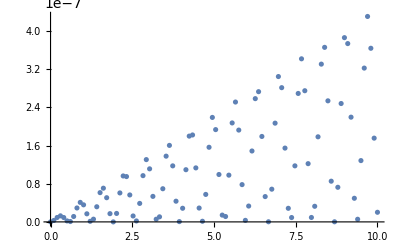

```mathematica
ListPlot[mat3[[Floor[dm/2]]],PlotRange->All,DataRange->{0,mmax},ImageSize->imgsize]
ListPlot[mat4[[Floor[dm/2]]],PlotRange->All,DataRange->{0,mmax},ImageSize->imgsize]
```

lpw

```mathematica
(* Mathematica notebook for spectra analysis 1d (ω). Following [Gibbon]'s lecture 4
  date : 10/12/2018
  author: Óscar L. Amaro
*)
```

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

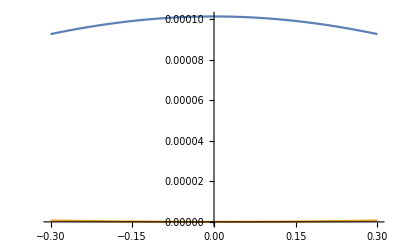

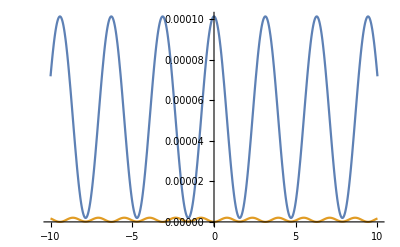

```mathematica
a0=1;(* low a0->1st mode dominates *)
ω0=1;
γ0=10;
q=a0/γ0;
ωR=ω0/γ0;
AwR=(ωR^2 a0^2)/(8 Pi);

dPdO=Function[m,(2 m^2 AwR)/γ0^2( (Cot[θR]/(2 q^2))^2 BesselJ[m,(√2) q m Sin[Abs[θR]]]^2 +(D[BesselJ[m,x],x]/.x->((√2) q m Sin[Abs[θR]]))^2)];
Plot[{dPdO[1],dPdO[2]},{θR,-3/γ0,3/γ0}]
Plot[{dPdO[1],dPdO[2]},{θR,-100/γ0,100/γ0}]
```

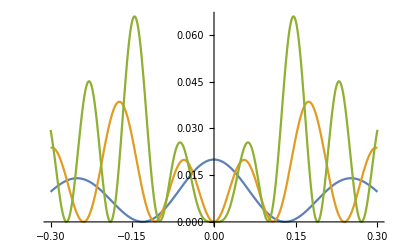

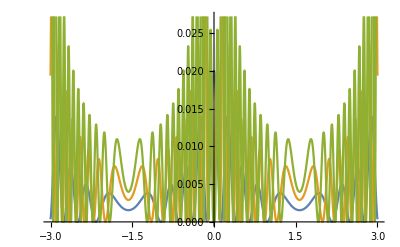

```mathematica
a0=100;(* hogh a0->higher modes dominate *)
ω0=1;
γ0=10;
q=a0/γ0;
ωR=ω0/γ0;
AwR=(ωR^2 a0^2)/(8 Pi);

dPdO=Function[m,(2 m^2 AwR)/γ0^2( (Cot[θR]/(2 q^2))^2 BesselJ[m,(√2) q m Sin[Abs[θR]]]^2 +(D[BesselJ[m,x],x]/.x->((√2) q m Sin[Abs[θR]]))^2)];
Plot[{dPdO[1],dPdO[2],dPdO[3]},{θR,-3/γ0,3/γ0}]
Plot[{dPdO[1],dPdO[2],dPdO[3]},{θR,-30/γ0,30/γ0}]
```

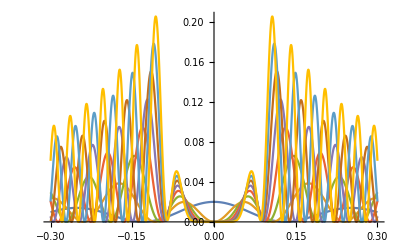

```mathematica
Plot[{dPdO[1],dPdO[2],dPdO[3],dPdO[4],dPdO[5],dPdO[6],dPdO[7],dPdO[8]},{θR,-3/γ0,3/γ0}]
```

```mathematica
a0=3(* high a0->higher modes dominate *)
ω0=1
γ0=3
mat=Table[dPdO[m],{m,10,1,-0.1},{θR,-3/γ0,3/γ0,0.011}];
```

3

1

3